```mathematica
Solve[{x*(1-x)-a1*x*y/(1+b1*x)==0,a1*x*y/(1+b1*x)-d1*y-a2*y*z/(1+b2*y)==0,a2*y*z/(1+b2*y)-d2*z==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.22208,y→0.125,z→-32.14},{x→0.,y→0.125,z→-5.},{x→0.0970874,y→0.219154,z→0.},{x→0.767535,y→0.125,z→12.8425},{x→1.,y→0.,z→0.},{x→0.,y→0.,z→0.}}

```mathematica
a1=5;
b1=2;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol1=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.75,y[0]==0.13,z[0]==13.8},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol1],{t,0,1000},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

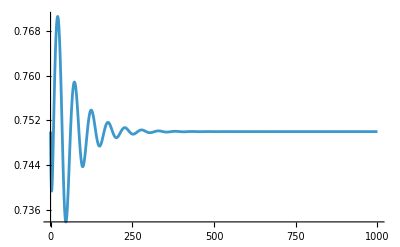

```mathematica
Plot[Evaluate[x[t]/.sol1],{t,0,1000},PlotRange->All]
```

```mathematica
j1={{D[x*(1-x)-a1*x*y/(1+b1*x),x],D[x*(1-x)-a1*x*y/(1+b1*x),y],D[x*(1-x)-a1*x*y/(1+b1*x),z]},{D[a1*x*y/(1+b1*x)-d1*y-a2*y*z/(1+b2*y),x],D[a1*x*y/(1+b1*x)-d1*y-a2*y*z/(1+b2*y),y],D[a1*x*y/(1+b1*x)-d1*y-a2*y*z/(1+b2*y),z]},{D[a2*y*z/(1+b2*y)-d2*z,x],D[a2*y*z/(1+b2*y)-d2*z,y],D[a2*y*z/(1+b2*y)-d2*z,z]}}/.{x->0.7675350240244827,y->0.125,z->12.842501092021944}
```

{{-0.621534,-1.4274,0},{0.0864639,0.20548,-0.01},{0,0.82192,1.73472×10^-18}}

```mathematica
Eigenvalues[j1]
```

{-0.434119+0. ⅈ,0.00903266+0.108102 ⅈ,0.00903266-0.108102 ⅈ}

```mathematica
a1=5;
b1=2.2;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol2=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.81,y[0]==0.11,z[0]==12.59},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,0,1000},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

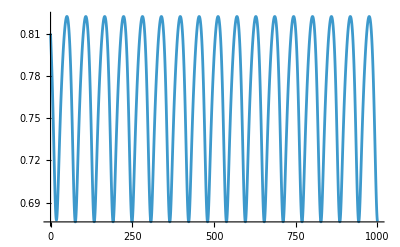

```mathematica
Plot[Evaluate[x[t]/.sol2],{t,0,1000},PlotRange->All]
```

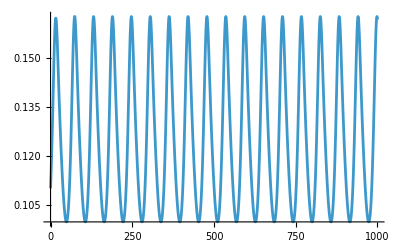

```mathematica
Plot[Evaluate[y[t]/.sol2],{t,0,1000},PlotRange->All]
```

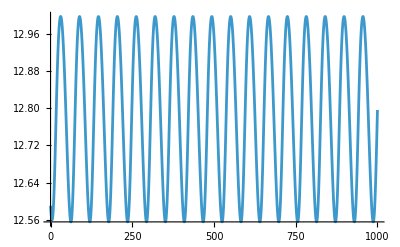

```mathematica
Plot[Evaluate[z[t]/.sol2],{t,0,1000},PlotRange->All]
```

```mathematica
a1=5;
b1=2.3;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol2=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.81,y[0]==0.11,z[0]==12.59},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,0,1000},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

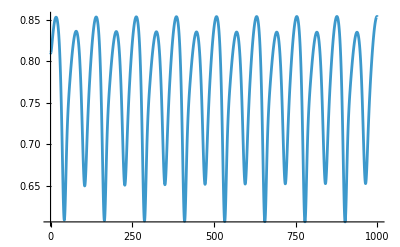

```mathematica
Plot[Evaluate[x[t]/.sol2],{t,0,1000},PlotRange->All]
```

```mathematica
a1=5;
b1=2.38;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol2=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.81,y[0]==0.11,z[0]==12.54},{x,y,z},{t,1000,2000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,1000,2000},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

```mathematica
Evaluate[{x[1000],y[1000],z[1000]}/.sol2]
```

{{0.844084,0.0932008,11.9197}}

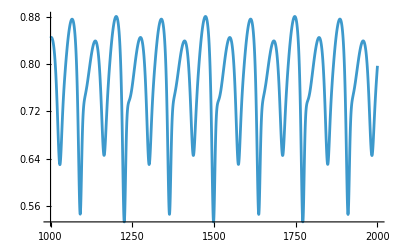

```mathematica
Plot[Evaluate[x[t]/.sol2],{t,1000,2000},PlotRange->All]
```

```mathematica
a1=5;
b1=3;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol2=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.81,y[0]==0.11,z[0]==12.54},{x,y,z},{t,1000,2000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,1000,2000},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

```mathematica
Evaluate[{x[1000],y[1000],z[1000]}/.sol2]
```

{{0.952874,0.0331404,9.7272}}

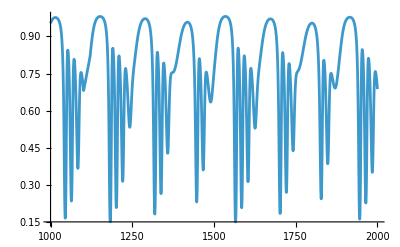

```mathematica
Plot[Evaluate[x[t]/.sol2],{t,1000,2000},PlotRange->All]
```

```mathematica
a1=5;
b1=3;
a2=0.1;
b2=2;
d1=0.4;
d2=0.01;
sol3=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.952874,y[0]==0.0331404,z[0]==9.7272},{x,y,z},{t,0,2000}];
```

```mathematica
sol4=NDSolve[{x'[t]==x[t]*(1-x[t])-a1*x[t]*y[t]/(1+b1*x[t]),y'[t]==a1*x[t]*y[t]/(1+b1*x[t])-d1*y[t]-a2*y[t]*z[t]/(1+b2*y[t]),z'[t]==a2*y[t]*z[t]/(1+b2*y[t])-d2*z[t],x[0]==0.952874,y[0]==0.0331404,z[0]==9.72721},{x,y,z},{t,0,2000}];
```

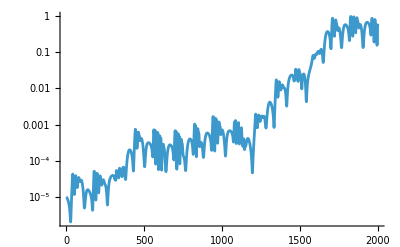

```mathematica
LogPlot[Sqrt[(Evaluate[x[t]/.sol3]-Evaluate[x[t]/.sol4])^2+(Evaluate[y[t]/.sol3]-Evaluate[y[t]/.sol4])^2+(Evaluate[z[t]/.sol3]-Evaluate[z[t]/.sol4])^2],{t,0,2000},PlotRange->All]
```

```mathematica
t1=Table[{t,Log[Sqrt[(Evaluate[x[t]/.sol3]-Evaluate[x[t]/.sol4])^2+(Evaluate[y[t]/.sol3]-Evaluate[y[t]/.sol4])^2+(Evaluate[z[t]/.sol3]-Evaluate[z[t]/.sol4])^2][[1]]]},{t,0,2000}];
```

```mathematica
t1[[5]]
```

{4,-11.561}

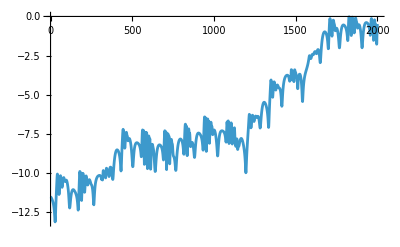

```mathematica
ListPlot[t1,Joined->True]
```

```mathematica
LinearModelFit[t1,x,x]
```

FittedModel[…]

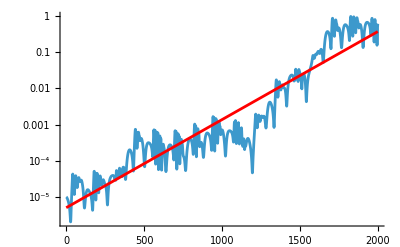

```mathematica
LogPlot[{Sqrt[(Evaluate[x[t]/.sol3]-Evaluate[x[t]/.sol4])^2+(Evaluate[y[t]/.sol3]-Evaluate[y[t]/.sol4])^2+(Evaluate[z[t]/.sol3]-Evaluate[z[t]/.sol4])^2],Exp[-12.2+0.00561*t]},{t,0,2000},PlotRange->All,PlotStyle->{Automatic,Red}]
```

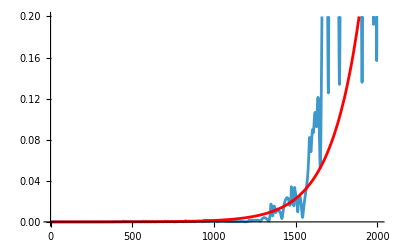

```mathematica
Plot[{Sqrt[(Evaluate[x[t]/.sol3]-Evaluate[x[t]/.sol4])^2+(Evaluate[y[t]/.sol3]-Evaluate[y[t]/.sol4])^2+(Evaluate[z[t]/.sol3]-Evaluate[z[t]/.sol4])^2],Exp[-12.2+0.00561*t]},{t,0,2000},PlotRange->{Automatic,{0,0.2}},PlotStyle->{Automatic,Red}]
```